```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"output"]
PoleFig100=Import["pole_fig100.dat","Table"];
PoleFig110=Import["pole_fig110.dat","Table"];
PoleFig111=Import["pole_fig111.dat","Table"];
```

D:\project_rust\MMUVP_ECM\output

```mathematica
points100=Partition[Flatten[PoleFig100],3];
Length[points100]
points110=Partition[Flatten[PoleFig110],3];
Length[points110]
points111=Partition[Flatten[PoleFig111],3];
Length[points111]
```

1000

1000

1000

```mathematica
Graphics3D[{Opacity[0.2],Sphere[{0,0,0}],Opacity[1],Point[points100],Red,Line[{{0,0,0},{1,0,0}}],Green,Line[{{0,0,0},{0,1,0}}],Blue,Line[{{0,0,0},{0,0,1}}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[0.2],Sphere[{0,0,0}],Opacity[1],Point[points110],Red,Line[{{0,0,0},{1,0,0}}],Green,Line[{{0,0,0},{0,1,0}}],Blue,Line[{{0,0,0},{0,0,1}}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[0.2],Sphere[{0,0,0}],Opacity[1],Point[points111],Red,Line[{{0,0,0},{1,0,0}}],Green,Line[{{0,0,0},{0,1,0}}],Blue,Line[{{0,0,0},{0,0,1}}]}]
```

-Graphics3D-

```mathematica
proection100XY = Table[{points100[[i,1]],points100[[i,2]]}/(1+Abs[points100[[i,3]]]),{i,1,Length[points100]}];
proection100XZ = Table[{points100[[i,1]],points100[[i,3]]}/(1+Abs[points100[[i,2]]]),{i,1,Length[points100]}];
proection100YZ = Table[{points100[[i,2]],points100[[i,3]]}/(1+Abs[points100[[i,1]]]),{i,1,Length[points100]}];
```

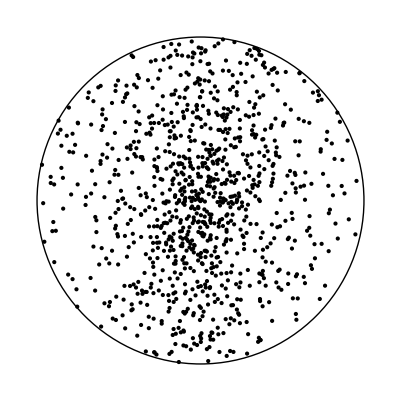
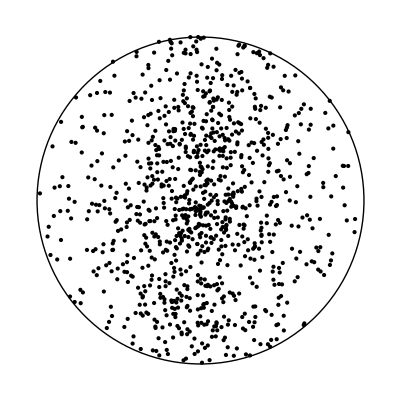
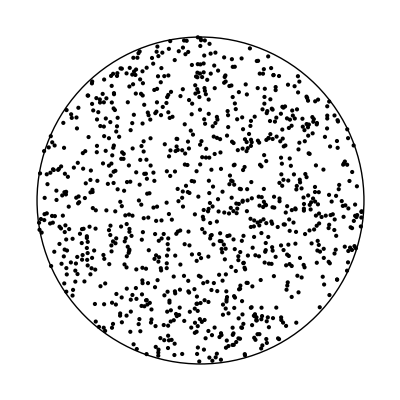

```mathematica
{Graphics[{Point[proection100XY],Circle[{0,0}]}],Graphics[{Point[proection100XZ ],Circle[{0,0}]}],Graphics[{Point[proection100YZ ],Circle[{0,0}]}]}
```

```mathematica
proection110XY = Table[{points110[[i,1]],points110[[i,2]]}/(1+Abs[points110[[i,3]]]),{i,1,Length[points110]}];
proection110XZ = Table[{points110[[i,1]],points110[[i,3]]}/(1+Abs[points110[[i,2]]]),{i,1,Length[points110]}];
proection110YZ = Table[{points110[[i,2]],points110[[i,3]]}/(1+Abs[points110[[i,1]]]),{i,1,Length[points110]}];
```

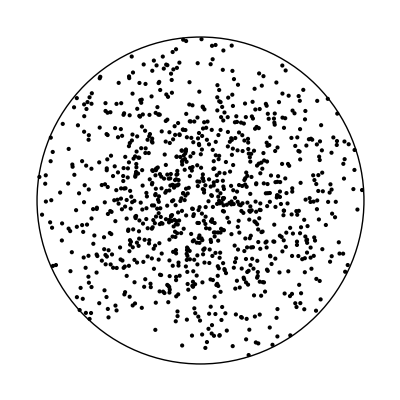
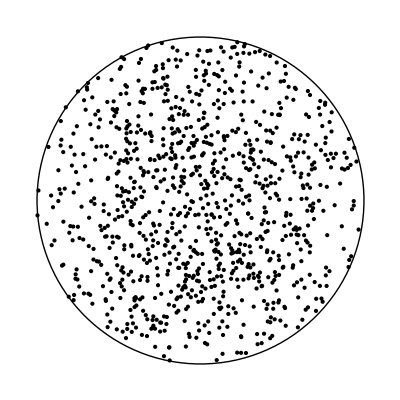
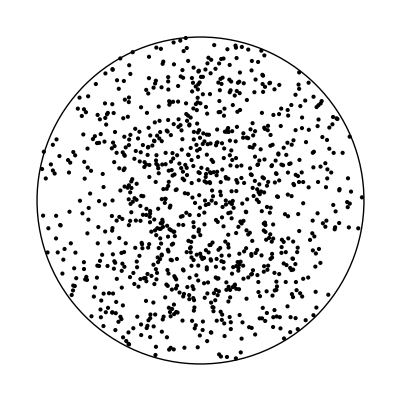

```mathematica
{Graphics[{Point[proection110XY],Circle[{0,0}]}],Graphics[{Point[proection110XZ ],Circle[{0,0}]}],Graphics[{Point[proection110YZ ],Circle[{0,0}]}]}
```

```mathematica
proection111XY = Table[{points111[[i,1]],points111[[i,2]]}/(1+Abs[points111[[i,3]]]),{i,1,Length[points111]}];
proection111XZ = Table[{points111[[i,1]],points111[[i,3]]}/(1+Abs[points111[[i,2]]]),{i,1,Length[points111]}];
proection111YZ = Table[{points111[[i,2]],points111[[i,3]]}/(1+Abs[points111[[i,1]]]),{i,1,Length[points111]}];
```

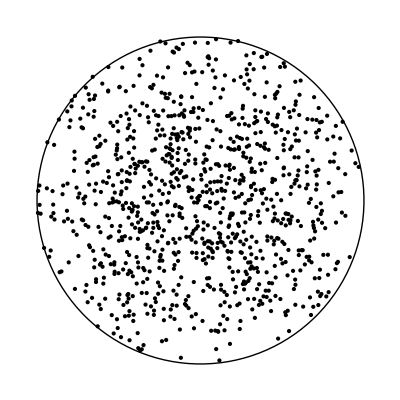
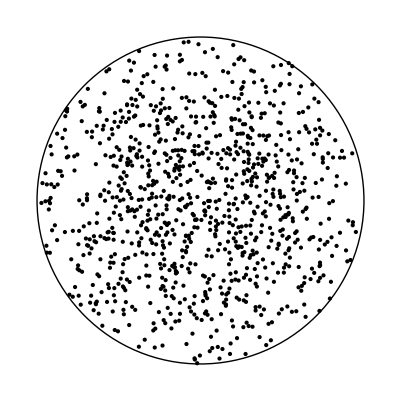
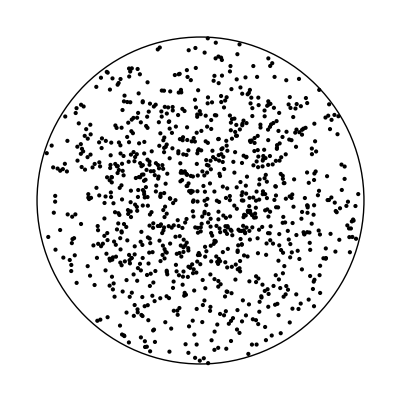

```mathematica
{Graphics[{Point[proection111XY],Circle[{0,0}]}],Graphics[{Point[proection111XZ ],Circle[{0,0}]}],Graphics[{Point[proection111YZ ],Circle[{0,0}]}]}
```